```mathematica
ShowGraph6[allGraphs_,key_]:=Labeled[
allGraphs[key,"graph"],
Row[{
Style["■",ColourForKey[allGraphs,key]],
MatrixPlot[
allGraphs6[key,"matrix"],
 ImageSize->30, 
FrameTicks->None,
ColorRules->{0-> White,1-> Darker[Gray],2-> Darker[Green]}
]
}
]
]
```

```mathematica
ShowGraph6b[allGraphs_,key_]:=Row[{
Style["■",ColourForKey[allGraphs,key]],
MatrixPlot[
allGraphs6[key,"matrix"],
 ImageSize->30, 
FrameTicks->None,
ColorRules->{0-> White,1-> Darker[Gray],2-> Darker[Green]}
]
}
]
```

```mathematica
Table[ShowGraph6[allGraphs6,k],{k,Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},allGraphs6[#,"vertexsets"]=={{1,3},{2,4},{5},{6}}&&VertexCount[g]==4&&EdgeCount[g]==5]&]}]
```

{-Graphics-■-Graphics-,-Graphics-■-Graphics-,-Graphics-■-Graphics-,-Graphics-■-Graphics-,-Graphics-■-Graphics-,-Graphics-■-Graphics-}

```mathematica
ShowGraph6[allGraphs6,K6Key]
```

-Graphics-■-Graphics-

```mathematica
MatrixForm[allGraphs6[K6Key,"matrix"]]
```

(2 | 1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 1 | 1
1 | 1 | 2 | 1 | 1 | 1
1 | 1 | 1 | 2 | 1 | 1
1 | 1 | 1 | 1 | 2 | 1
1 | 1 | 1 | 1 | 1 | 2)

```mathematica
Table[ShowGraph6b[allGraphs6,k],{k,allGraphs6AtomKeys}]
```

{■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-}

```mathematica
Table[ShowGraph6b[allGraphs6,k],{k,allGraphs6NullAtomKeys}]
```

{■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-}

```mathematica
Table[ShowGraph6b[allGraphs5,k],{k,allGraphs5AtomKeys}]
```

{■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-}

```mathematica
Table[ShowGraph6b[allGraphs4,k],{k,allGraphs4AtomKeys}]
```

{■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-}

```mathematica
Table[ShowGraph6b[allGraphs4,k],{k,allGraphs4NullAtomKeys}]
```

{■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-,■-Graphics-}

```mathematica
rep6=Table[allGraphs6[k,"colofour"]->ShowGraph6[allGraphs6,k],{k,allGraphs6AtomKeys}];
```

```mathematica
rep6E=Table[allGraphs6[k,"colofourrealnull"]->ShowGraph6[allGraphs6,k],{k,allGraphs6NullAtomKeys}];
```

```mathematica
ShowGraph6[allGraphs6,8774605]
```

-Graphics-■-Graphics-

```mathematica
allGraphs6[8774605,"colofour"]/.rep6
```

-Graphics-■-Graphics-+-Graphics-■-Graphics-

```mathematica
allGraphs6[8774605,"colofourrealnull"]/.rep6E
```

-4 -Graphics-■-Graphics-+-Graphics-■-Graphics-+-Graphics-■-Graphics-+2 -Graphics-■-Graphics-+2 -Graphics-■-Graphics-+-Graphics-■-Graphics-+-Graphics-■-Graphics---Graphics-■-Graphics---Graphics-■-Graphics---Graphics-■-Graphics---Graphics-■-Graphics---Graphics-■-Graphics-+-Graphics-■-Graphics-

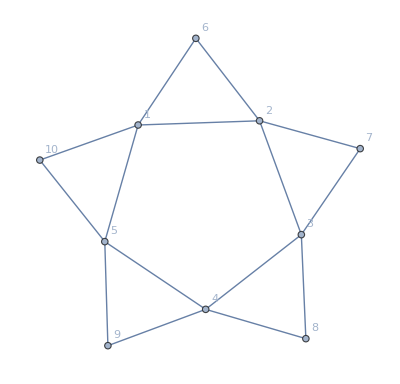

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,1<->6,6<->2,2<->7,7<->3,8<->3,8<->4,9<->4,9<->5,10<->5,10<->1},VertexLabels->"Name"]
```

```mathematica
Table[Framed[ShowGraph6[allGraphs6,k]->TableForm[Table[Table[ShowGraph6b[allGraphs6,c],{c,child}],{child,allGraphs6[k,"children"]}]]],{k,RandomSample[Keys[allGraphs6],20]}]
```

{-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-,-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-,-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-,-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-,-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-,-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-,-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-,-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-,-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-,-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-,-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-,-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-,-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-,-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-,-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-,-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-,-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-,-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-,-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-,-Graphics-■-Graphics-→■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-
■-Graphics- | ■-Graphics-}